### Kermack-McKendrick model with 2 pathogens

n(t,-,-) | susceptibles
n(t,x_1,-) | infecteds with pathogen 1 x_1 days ago
n(t,-,x_2) | infecteds with pathogen 2 time x_2 days ago
n(t,x_1,x_2) | coinfecteds: x_1 days path 1, x_2 days path 2
B | birth rate (susceptible)
μ(x_1,x_1) | death rate: x_1 days path 1, x_2 days path 2
β_i(x) | susceptibility path i: x days infected with other path
λ_i(t) | infection force path i
κ_i(x_1,x_2) | infectivity path i: x_1 days path 1, x_2 days path 2

d/dt n(t,-,-)=B-(μ(0,0)+β_1(0)λ_1(t)+β_2(0)λ_2(t))n(t,-,-)
λ_1(t)=∫_0^∞ κ_1(x_1,0)n_1(t,x_1)+∫_0^∞ κ_1(x_1,x_2)n_12(t,x_1,x_2)ⅆ x_2ⅆ x_1
λ_2(t)=∫_0^∞ κ_2(0,x_2)n_2(t,x_2)+∫_0^∞ κ_2(x_1,x_2)n_12(t,x_1,x_2)ⅆ x_1ⅆ x_2
∂/(∂t)n(t,x_1,-)+∂/(∂x_1)n(t,x_1,-)+(β_2(x_1)λ_2(t)+μ(x_1,-))n(t,x_1,-)=0
∂/(∂t)n(t,-,x_2)+∂/(∂x_2)n(t,-,x_2)+(β_1(x_2)λ_1(t)+μ(0,x_2))n(t,-,x_2)=0
∂/(∂t)n(t,x_1,x_2)+∂/(∂x_1)n(t,x_1,x_2)+∂/(∂x_2)n(t,x_1,x_2)+μ(x_1,x_2)n(t,x_1,x_2)=0
n(t,0,-)=β_1(0)λ_1(t)n(t,-,-)
n(t,-,0)=β_2(0)λ_2(t)n(t,-,-)
n(t,0,-)=β_1(x_2)λ_1(t)n(t,-,x_2)
c(t,-,0)=β_2(x_1)λ_2(t)n_1(t,x_1,-)

```mathematica
ClearAll["Global`*"]
outputdirectory=NotebookDirectory[]<>"exports/";
font="Latin Modern Roman";
```

```mathematica
(*run simulations
run R0s
find good parameters
make plots nice
make plot for parameter vs R01, R02, R12, R21 & final n sizes
write appendix
choose plot for main text
add text in main text
add text to response letter*)
```

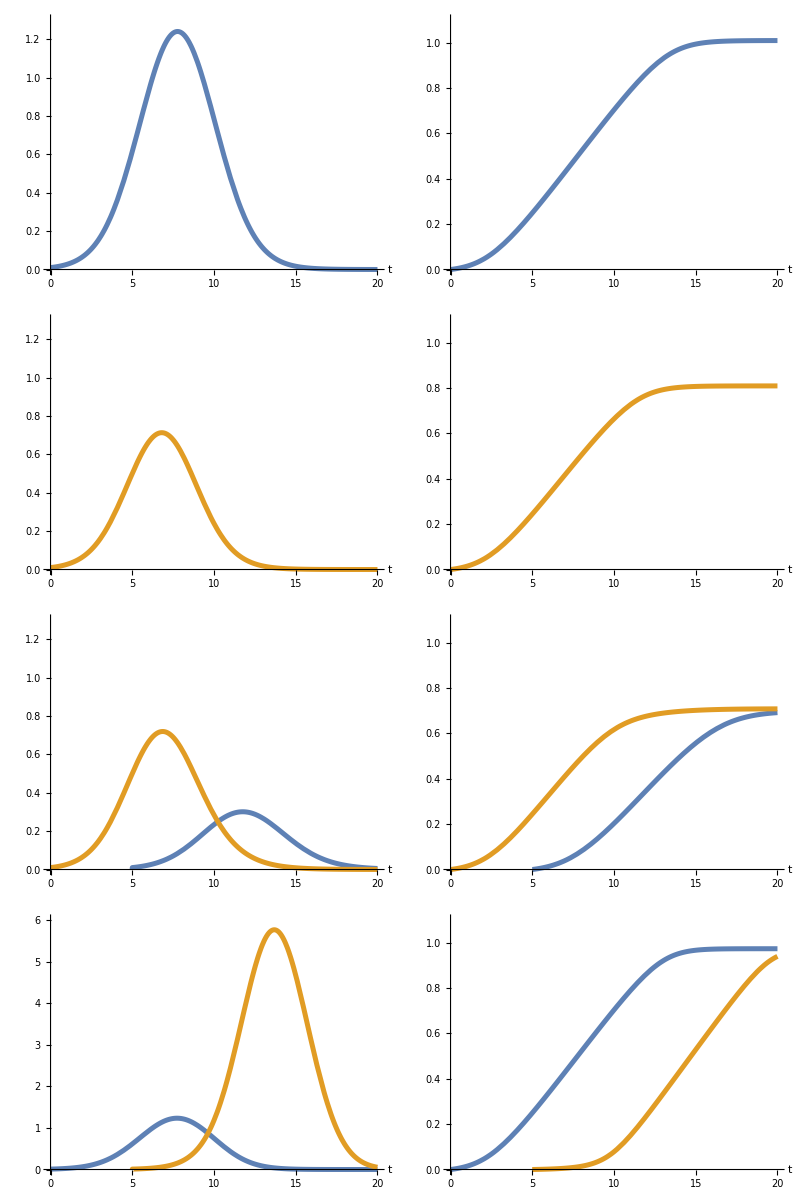
Pathogen 1 | -Graphics- |    | Immune response 1 | -Graphics-
Pathogen 2 | -Graphics- |    | Immune response 2 | -Graphics-
-Graphics-

```mathematica
(*within host simulations*)
{r1=1,r2=1,c11=2,c12=.5,c22=2.5,c21=0 ,pintro=10^-2,h11=10,h12=0,h21=10,h22=10};
withinvars={"p_1","p_2","b_1","b_2"};
sim[x1_?NumberQ,x2_?NumberQ]:=Module[{t,p1,p2,b1,b2,eqs,inis,sol,vars,events,tmin,f1,f2,tmax},
tmin=-Max[x1,x2]-.001;tmax=0;
f1[p1_,p2_]:=p1/(1+h11 p1+h12 p2);
f2[p1_,p2_]:=p2/(1+h21 p1+h22 p2);
eqs=
{
p1'[t]==(r1-c11 b1[t]-c12 b2[t]) p1[t]+DiracDelta[t+x1]pintro,
p2'[t]==(r2 -c21 b1[t]-c22 b2[t])p2[t]+DiracDelta[t+x2]pintro,
b1'[t]==f1[p1[t],p2[t]],
b2'[t]==f2[p1[t],p2[t]]
};
inis=
{
p1[tmin]==0,
p2[tmin]==0,
b1[tmin]==0,
b2[tmin]==0
};
vars={p1,p2,b1,b2};
#[[1]]->#[[2]]&/@Transpose[{withinvars,vars}]/.NDSolve[Join[eqs,inis],vars,{t,tmin,tmax}][[1]]
];
styles={ImageSize->Small,AxesLabel->{"t"},ImagePadding->{{20,15},{18,5}},LabelStyle->12,AxesOrigin->{0,0},RegionFunction->(#2>0&),PlotStyle->Thickness[.02]};
withinplots[x1_,x2_,{maxp_,maxb_}]:=Module[{sol=sim[x1,x2],tmax},
tmax=Max[x1,x2];
{
Plot[{"p_1"[t-tmax]/.sol,"p_2"[t-tmax]/.sol},{t,0,tmax}(*,PlotLegends->{"p_1","p_2"}*),PlotRange->{.0,maxp},Evaluate@styles,AxesLabel->{"t"}],
Plot[{"b_1"[t-tmax]/.sol,"b_2"[t-tmax]/.sol},{t,0,tmax}(*,PlotLegends->{"b_1","b_2"}*),PlotRange->{.0,maxb},Evaluate@styles,PlotStyle->Dashed]}];
maxpb1={1.4,1.2};
maxpb2={15,1};
line[col_,options_]:=Plot[.5,{x,0,1},PlotStyle->{Thickness[.14],ColorData[97][col],options},Axes->None,ImageSize->20,PlotRange->{0,1}];
dashstyle=Dashing[.3];
legendwithinhost=Style[Framed[Grid[{{"Pathogen 1",line[1,Nothing],"  ","Immune response 1",line[1,dashstyle]},{"Pathogen 2",line[2,Nothing],"  ","Immune response 2",line[2,dashstyle]}},Alignment->{Center,Center}],RoundingRadius->2],FontFamily->font,11.5];
(Export[outputdirectory<>"within-host-simulations.pdf",#];#)&@Column[{legendwithinhost,
Grid[{
withinplots[20,0,{1.3,1.1}],
withinplots[0,20,{1.3,1.1}],
withinplots[15,20,{1.3,1.1}],
withinplots[20,15,{6,1.1}]
}]},Alignment->Center]
```

```mathematica
Clear[final];
final[x1_,x2_]:=final[x1,x2]=Evaluate@Module[{sol=sim[x1,x2]},Table[var->(var[0]/.sol),{var,withinvars}]];
(*final[.0001,20]*)
```

```mathematica
(*pde functions*)
(*birth rate*)
B= 1;
(*mortality*)
μs=0.02;μ1=.01;μ2=.001;
(*coinfection effect on mortality*)
θμ=.001;
(*max length of infection -> cutoff and then immune TO DO AGAIN?!*)
τ=20;
(*mortality*)
μ[x_?NumberQ,y_?NumberQ]:=μs+ (μ1 "p_1"+ μ2 "p_2")/.final[x,y];
(*infectivity*)
κ1c=1;
κ2c=1;
κ1[x_?NumberQ,y_?NumberQ]:=κ1c "p_1"/.final[x,y];
(*check if that's right or swap x and y*)
κ2[x_?NumberQ,y_?NumberQ]:=κ2c"p_2"/.final[x,y];
(*susceptibility*)
β1c=.01;
β2c=.005;
β1[x_?NumberQ]:=β1c ⅇ^(-c12 "b_2"/.final[0,x]);
β2[x_?NumberQ]:=β2c ⅇ^(-c21 "b_1"/.final[x,0]);
```

```mathematica
(*SetDirectory["/home/spc/Documents/latex_neu/epidemics elsarticle/images"];*)
```

```mathematica
styleall={BaseStyle->{FontFamily->font}};
xmax=22;
```

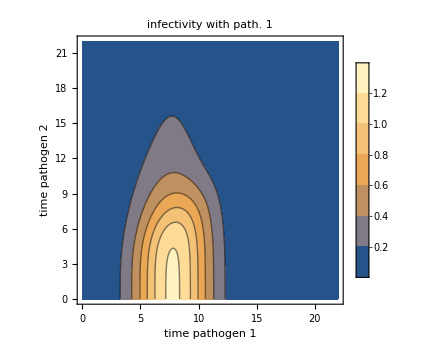
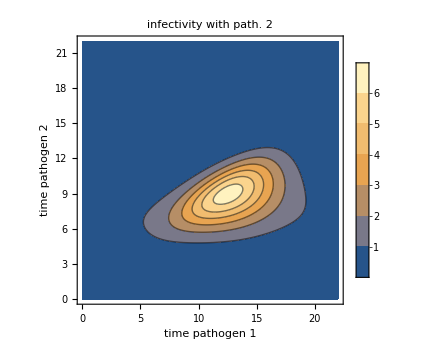

```mathematica
Column@Table[(Export[outputdirectory<>"within-host-infectivity-contourplot-"<>ToString[κ/.{κ1->1,κ2->2}]<>".pdf",#];#)&@ContourPlot[κ[x,y],{x,0,xmax},{y,0,xmax},PlotLabel->("infectivity with path. "<>(κ/.{κ1->"1",κ2->"2"})),FrameLabel->{"time pathogen 1","time pathogen 2"},PlotLegends->Automatic,LabelStyle->18,(*Exclusions->{{x==τ,y==τ}},*)Evaluate@styleall,ImageSize->Medium,PlotRange->All(*,Contours->Range[.3,2,.3]*),MaxRecursion->4
],{κ,{κ1,κ2}}]
```

```mathematica
(*(Export["coinf_susceptibility.pdf",#,"PDF"];#)&@Plot[{β1[x],β2[x]},{x,0,xmax},PlotRange->Full,AxesOrigin->{0,0},PlotLegends->Placed[LineLegend[Style[#,FontFamily->font]&/@{"pathogen 1","pathogen 2"},LegendFunction->"Frame",FrameStyle->Black],{{.65,.8},{.3,.5}}],AxesLabel->{"day"},ImageSize->Medium,PlotLabel->"susceptibility",LabelStyle->18,Evaluate@styleall]*)
```

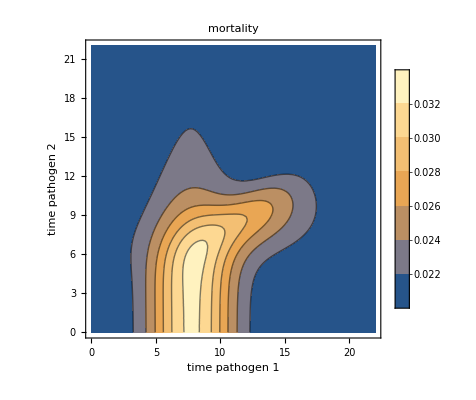

```mathematica
(Export[outputdirectory<>"within-host-mortality-contourplot.pdf",#];#)&@ContourPlot[μ[x,y],{x,0,xmax},{y,0,xmax},PlotLabel->"mortality",FrameLabel->{"time pathogen 1","time pathogen 2"},PlotLegends->Automatic,LabelStyle->18,PlotRange->All(*,Contours->Range[.023,.034,.003]*),Evaluate@styleall,MaxRecursion->4
]
```

#### Implementation : Escalator Boxcar Train

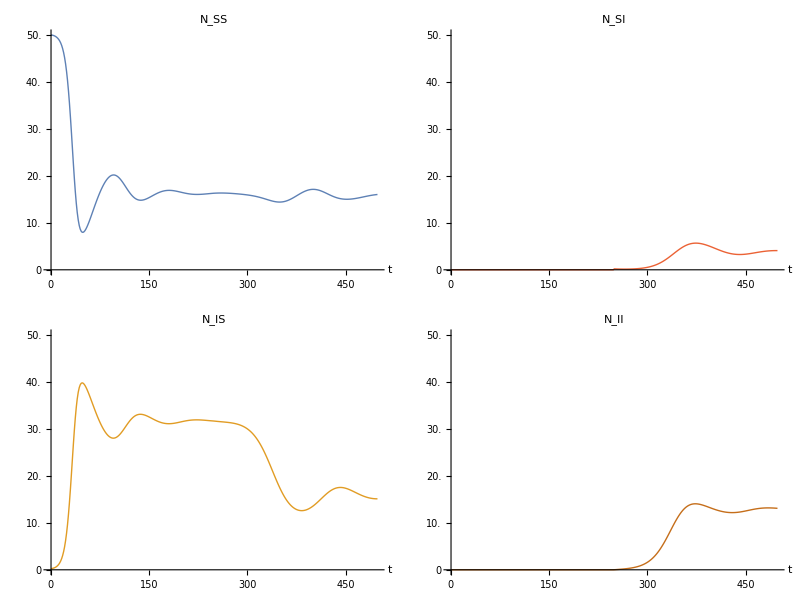

```mathematica
(*time steps: train schedule*)
(*choose T1=T2 for now!*)
T=15;
T1=T2=T;
Δt=τ/(T-1.5);
(*o[t_?NumericQ][x_]:=x;*)
(*train changes*)
R=ArrayFlatten[SparseArray[{
(*susceptibles stay susceptible*)
{1,1,1,1}->1,
(*block at end of infected matrix*)
{1,1,T2,T2}->1,
{T1,T1,1,1}->1,
{T1,T1,T2,T2}->1,
(*from j to i for pathogen 2*)
{x_,x_,i_,j_}/;(x==T1∨x==1)∧j>1∧i==j+1->1,
(*from j to i for pathogen 1*)
{i_,j_,x_,x_}/;(x==T2∨x==1)∧j>1∧i==j+1->1,
(*from j to i for path 1 and l to k for path 2*)
{i_,j_,k_,l_}/;j>1∧i==j+1∧l>1∧k==l+1∧j<T1∧l<T2->1
},{T1,T1,T2,T2}]];
(*mortality*)
ij[i_,j_]:={Δt (i-3/2),Δt (j-3/2)};
m=ArrayFlatten[SparseArray[{i_,i_,j_,j_}->μ@@ij[i,j],{T1,T1,T2,T2}]];
(*infection force*)
ϕ1=Flatten[SparseArray[{1,i_,1,j_}/;i>1->(κ1@@ij[i,j]),{1,T1,1,T2}]];
ϕ2=Flatten[SparseArray[{1,i_,1,j_}/;j>1->κ2@@ij[i,j],{1,T1,1,T2}]];
(*infection vector*)
q1=ArrayFlatten[SparseArray[{
{2,1,i_,i_}-> β1[Δt (i-3/2)],
{1,1,i_,i_}->-β1[Δt (i-3/2)]
},{T1,T1,T2,T2}]];
q2=ArrayFlatten[SparseArray[{
{i_,i_,2,1}->β2[Δt (i-3/2)],
{i_,i_,1,1}->-β2[Δt (i-3/2)]
},{T1,T1,T2,T2}]];
b=Normal@Flatten[SparseArray[{1,1,1}->B,{T1,1,T2}]];

solve[n0_,pert_,tmax_]:=NDSolve[
{
n'[t]==b-m.n[t]+ q1.n[t]ϕ1.n[t]+q2.n[t] ϕ2.n[t],
n[0]==n0,
WhenEvent[Mod[t, Δt]==0,n[t]->R.n[t]],
WhenEvent[t==pert[[1]],n[t]->n[t]+pert[[2]]]
},
n,
{t,0,tmax}];
s00=B/μ[0,0];
n0=Normal[Flatten[SparseArray[{
{1,1,1}->s00,
{x1_,1,1}->.01Δt},
{T1,1,T2}]]];
n0pert=Normal[Flatten[SparseArray[{
{1,1,x_}/;x>1-> .01Δt},
{T1,1,T2}]]];
tickfun[number_][min_,max_]:=N[FindDivisions[{min,max},number],1];
Clear[style];
style[col_,title_,tmin_]:={PlotRange->{0,s00},PlotLabel->title,AxesOrigin->{tmin,0},PlotStyle->{ColorData[97][col],Thick},AxesLabel->{"t"},LabelStyle->11,
ImageSize->{200,Automatic},
ImagePadding->{{35,12},{Automatic,Automatic}},PlotPoints->( Floor[tmax/Δt]),MaxRecursion->0,Ticks->{Automatic,tickfun[5]},
styleall};
plot[sol_,tmin_,tmax_]:=Column[{
Grid[Transpose@{
{
Plot[Flatten[SparseArray[{1,1,1,1}->1,{1,T1,1,T2}]].(n[t]/.sol[[1]]),{t,tmin,tmax},Evaluate@style[1,"N_SS",tmin]],
Plot[ArrayFlatten[SparseArray[{1,i_,1,1}/;i>1->1,{1,T1,1,T2}]].(n[t]/.sol[[1]]),{t,tmin,tmax},Evaluate@style[2,"N_IS",tmin]]
},
{
Plot[ArrayFlatten[SparseArray[{1,1,1,i_}/;i>1->1,{1,T1,1,T2}]].(n[t]/.sol[[1]]),{t,tmin,tmax},Evaluate@style[4,"N_SI",tmin]],
Plot[ArrayFlatten[SparseArray[{1,i_,1,j_}/;i>1∧j>1->1,{1,T1,1,T2}]].(n[t]/.sol[[1]]),{t,tmin,tmax},Evaluate@style[6,"N_II",tmin]]

}}
]
}] ;
tmax=500;
sol=solve[n0,{Δt Floor[tmax/2/Δt],n0pert},tmax];(Export[outputdirectory<>"simulation.pdf",#];#)&@plot[sol,Δt.5,Δt Floor[tmax/Δt]-Δt.5]
```

```mathematica
(*one at eq*)
n0=Normal[Flatten[SparseArray[{
{1,1,1}->s00,
{x1_,1,1}->.00001Δt(*,
{x1_,1,1}->.0001Δt,
*)
(*
{x1_,1,1}/;T1>x1>1->n10[(x1-3/2) Δt]Δt,
{T1,1,1}->NIntegrate[n10[x1],{x1,T1 Δt,∞}],
{y_,1,x_}/;x>1->.0001Δt*)},
{T1,1,T2}]]];
n0pert=Normal[Flatten[SparseArray[{
{1,1,x_}/;x>1-> .0001Δt},
{T1,1,T2}]]];
```

```mathematica
(*
tmaxF=10τ;
F1=NDSolveValue[{F'[y]==-μ[y,0]F[y],F[0]==1},F,{y,0,tmaxF}];
*)
F1[x1_?NumericQ,λ2_?NumericQ]:=E^(-NIntegrate[μ[y,0]+β2[y]λ2,{y,0,x1}]);
s10=1/NIntegrate[β1[0]κ1[x1,0]F1[x1,0],{x1,0,∞}];
λ10=(B-μ[0,0]s10)/(β1[0] s10);
n10[x1_]:= λ10 β1[0] s10 F1[x1,0];
AbsoluteTiming[Row[{"R_0^1 ",NIntegrate[β1[0]κ1[x1,0]F1[x1,0] s00,{x1,0,∞}]}]]
```

$Aborted

$Aborted

```mathematica
F2[x2_?NumericQ,λ1_?NumericQ]:=E^(-NIntegrate[μ[0,y]+β1[y]λ1,{y,0,x2}]);
s20=1/NIntegrate[β2[0]κ2[0,x2]F2[x2,0],{x2,0,τ}];
```

```mathematica
λ20=(B-μ[0,0]s20)/(β2[0] s20);
n20[x2_]:= λ20 β2[0] s20 F2[x2,0];
s00=B/μ[0,0];
AbsoluteTiming[Row[{"R_0^2 ",NIntegrate[β2[0]κ2[0,x2]F2[x2,0] s00,{x2,0,τ}]}]]
```

{0.218346,R_0^2 0.849662}

```mathematica
(*can 2 invade 1?*)
```

```mathematica
F12[x1_?NumericQ,x2_?NumericQ]:=E^(-NIntegrate[μ[x1-x2+σ,σ],{σ,0,x2}]);
F21[x1_?NumericQ,x2_?NumericQ]:=E^(-NIntegrate[μ[σ,x2-x1+σ],{σ,0,x1}]);
RD12A=β2[0]s10 NIntegrate[F2[x2,λ10]κ2[0,x2],{x2,0,∞},PrecisionGoal->2];
QD1[x2_?NumericQ]:=NIntegrate[κ2[x1,x1+x2]F21[x1,x1+x2],{x1,0,τ},PrecisionGoal->2];
RD12B=β2[0]s10 λ10 NIntegrate[β1[x2]F2[x2,λ10]QD1[x2],{x2,0,τ},PrecisionGoal->2];
QD2[η_?NumericQ]:=NIntegrate[κ2[x2+η,x2]F12[x2+η,x2],{x2,0,τ},PrecisionGoal->2];
RD12C=NIntegrate[β2[η]n10[η]QD2[η],{η,0,∞},PrecisionGoal->2];
RD12=RD12A+RD12B+RD12C
```

1.29741

```mathematica
(*^^ add timing*)
```

```mathematica
(*can 1 invade 2?*)
F1[x2_?NumericQ]:=E^(-NIntegrate[μ[y1,0]+λ20 β2[y1],{y1,0,x2}]);
RD21A=β1[0]s20 NIntegrate[F1[x1,λ20]κ1[x1,0],{x1,0,∞},PrecisionGoal->2];
Q21D1[x2_?NumericQ]:=NIntegrate[κ1[x1+x2,x1]F12[x1+x2,x2],{x1,0,τ},PrecisionGoal->2];
RD21B=β1[0]s20 λ20 NIntegrate[β2[x1]F1[x1,λ20]Q21D1[x1],{x1,0,τ},PrecisionGoal->2];
Q21D2[η_?NumericQ]:=NIntegrate[κ1[x1,x1+η]F21[x1,x1+η],{x1,0,τ},PrecisionGoal->2];
RD21C=NIntegrate[β1[η]n20[η]Q21D2[η],{η,0,∞},PrecisionGoal->2];
RD21=RD21A+RD21B+RD21C
(*NA IF Subscript[R, 2,0]<1!!*)
```

$Aborted

3.89022+RD21C

```mathematica
(*pedagoical example, not an epidemiological model*)
```

```mathematica
(*check if other papers in TPB have appendices*)
(*put infectivity plots and trajectories in main text*)
(*put table with R0's in main text*)
```